```mathematica
ClearAll["Global`*"]
ColorFun=Function[{x},ColorData["DarkBands"][x]];
ColorFun=Function[{x},ColorData["TemperatureMap"][x]];
Delta=1;
xi=0;
mx[x_]:=-Tanh[x/Delta];
my[x_]:=Sech[x/Delta]Cos[xi];
mz[x_]:=Sech[x/Delta]Sin[xi];
```

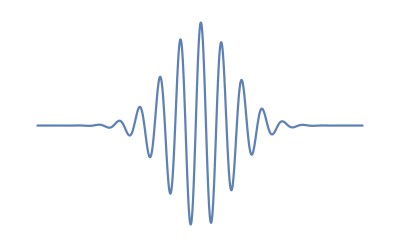

```mathematica
F[x_]:=Exp[-0.5(x-5)^2](Cos[10x])+0.5;
Plot[F[x]*0.1,{x,0,10},PlotRange->Full,ColorFunctionScaling->False, Axes->False,PlotRange->Full]
```

```mathematica
R=0.5;cylinder=ParametricPlot3D[{x,R Cos[theta],R Sin[theta]},{theta,-Pi,Pi},{x,-5,8},Mesh->None,ColorFunction->Function[{x,y},ColorData["ThermometerColors"][F[x]]],ColorFunctionScaling->False]
```

-Graphics3D-

```mathematica
xs=Table[{ColorFun[mx[i]],Arrow[Tube[{{i,-my[i]/2,0},{i+mx[i],my[i]/2,0}},0.04]]},{i,-5,8,1}];
ys=Table[Style[xs[[i]],Antialiasing->True],{i,1,Length[xs]}];
fig1=Graphics3D[{{Arrowheads[0.05],xs},{Opacity[0.2],cylinder[[1]]},{Opacity[0.5],Darker[Red],Arrowheads[0.03],Arrow[Tube[{{-4,1.3,0},{-2,1.3,0}},0.03]]}},ImageSize->1000,Axes->False,Boxed->False,ViewVector->{{10,-80,-100},{0,0,0}}]
```

-Graphics3D-

```mathematica
fig2=ParametricPlot3D[{x,1.3+F[x]*.3,0},{x,2,8},PlotRange->Full, Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
fig=Show[fig1,fig2]
```

-Graphics3D-

```mathematica
filename=FileNameJoin[{NotebookDirectory[],"dw_gaussian.pdf"}];
Export[filename,fig,ImageResolution->200];
```